## Differences between primes

```mathematica
Get[StringJoin[NotebookDirectory[] , "nprimes.mx"]]
```

```mathematica
primes=(#[[1]]^2*#[[2]]^4)&/@Permutations[Table[Prime[x],{x,200}],{2}]//Sort
```

{144,324,400,784,1936,2025,2500,2704,3969,4624,5625,5776,8464,9604,9801,13456,13689,15376,21609,21904,23409,26896,29241,29584,30625,35344,42849,44944,55696,58564,59536,60025,68121,71824,75625,77841,80656,85264,99856,105625,110224,110889,114244,126736,131769,136161,39708,2863445295800589361,2868097102343226961,2878073084734240849,2881248700870194769,2901829055063287561,2906116098044766721,2909728745608046209,2916224320321010689,2920952385249883609,2921781867197558401,2928212787897409609,2931389092384620169,2940248467459464529,2961098927192378449,2963851741066278241,2967028666657341049,2968636299877663801,2969311702392413569,2974160782818838369,2980460540554675369,3000149739154205089,3007988025672537961,3019555376665130521,3025974456210611929,3029805075316459729,3050314655704090009,3059582076874199881,3061213580620202569,3067747552478798281,3081229809467909089,3081436241287668289,3090749095559285449,3111895063527554929,3120366619757490601,3122074055217437329,3122692486280560561,3152152831827884329,3164086354053076321,3184100122675661809,3206449171771781329,3226947077459739841,3227631272216755849,3238143699159898369,3281067968104191409,3291754438893802729,3313500073840609249}
 |  |  |  |

```mathematica
primes=primes[[;;10000]]
```

```mathematica
n=15;results={};
```

## Prime 15

```mathematica
diffs = Table[primes[[n+1]]-primes[[n]],{n,Length@primes-1}];
series=Table[{x,diffs[[x]]},{x,Length@diffs}];
```

## Visibility Graph

```mathematica
natLinks =naturalVisibility[series];
```

## Graph

```mathematica
igv15=Graph[natLinks, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igv15];
```

```mathematica
count = Total[adj]//Counts
```

<|83→2,80→2,66→17,52→33,79→3,45→42,89→4,65→17,93→1,61→10,70→8,95→1,71→5,99→1,98→2,126→1,168→1,142→2,206→1,118→1,261→1,85→2,229→1,86→4,90→1,100→1,120→1,108→1,264→1,114→1,276→1,310→1,293→1,384→1,410→1,437→1,182→1,213→1,341→1,477→1,482→1,577→1,568→1,513→1,197→1,131→1,475→1,536→2,595→1,648→1,736→1,709→1,746→1,94→1,787→1,205→1,724→1,844→1,923→1,968→1,976→1,1006→1,1004→1,1017→1,1038→1,1073→1,1179→1,1240→1,1207→1,1224→1,1414→1,1488→1,1551→1,1601→1,520→1,1682→1,1687→1,1738→1,1876→1,1913→1,1933→1,1987→1,2054→1,2142→1,2231→1,2276→1,51→22,48→24,46→26,81→3,82→4,77→6,54→12,41→20,78→5,53→24,50→33,39→30,76→2,37→30,69→12,67→12,73→3,60→7,58→16,49→24,43→20,75→1,44→28,63→12,72→5,47→20,56→17,62→9,68→5,64→14,74→5,38→48,55→18,34→37,59→15,57→13,40→19,32→47,36→38,31→48,84→2,92→1,33→32,30→37,35→31,29→36,42→20,25→53,28→39,27→25,19→90,22→72,26→52,20→87,21→80,23→67,17→107,15→114,24→63,18→115,16→105,13→153,14→117,8→415,12→186,10→270,7→582,9→331,11→231,6→792,5→1030,4→1354,3→1449,2→902|>

```mathematica
count[1]=.
```

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}]
```

{{83,2/9999},{80,2/9999},{66,17/9999},{52,1/303},{79,1/3333},{45,14/3333},{89,4/9999},{65,17/9999},{93,1/9999},{61,10/9999},{70,8/9999},{95,1/9999},{71,5/9999},{99,1/9999},{98,2/9999},{126,1/9999},{168,1/9999},{142,2/9999},{206,1/9999},{118,1/9999},{261,1/9999},{85,2/9999},{229,1/9999},{86,4/9999},{90,1/9999},{100,1/9999},{120,1/9999},{108,1/9999},{264,1/9999},{114,1/9999},{276,1/9999},{310,1/9999},{293,1/9999},{384,1/9999},{410,1/9999},{437,1/9999},{182,1/9999},{213,1/9999},{341,1/9999},{477,1/9999},{482,1/9999},{577,1/9999},{568,1/9999},{513,1/9999},{197,1/9999},{131,1/9999},{475,1/9999},{536,2/9999},{595,1/9999},{648,1/9999},{736,1/9999},{709,1/9999},{746,1/9999},{94,1/9999},{787,1/9999},{205,1/9999},{724,1/9999},{844,1/9999},{923,1/9999},{968,1/9999},{976,1/9999},{1006,1/9999},{1004,1/9999},{1017,1/9999},{1038,1/9999},{1073,1/9999},{1179,1/9999},{1240,1/9999},{1207,1/9999},{1224,1/9999},{1414,1/9999},{1488,1/9999},{1551,1/9999},{1601,1/9999},{520,1/9999},{1682,1/9999},{1687,1/9999},{1738,1/9999},{1876,1/9999},{1913,1/9999},{1933,1/9999},{1987,1/9999},{2054,1/9999},{2142,1/9999},{2231,1/9999},{2276,1/9999},{51,2/909},{48,8/3333},{46,26/9999},{81,1/3333},{82,4/9999},{77,2/3333},{54,4/3333},{41,20/9999},{78,5/9999},{53,8/3333},{50,1/303},{39,10/3333},{76,2/9999},{37,10/3333},{69,4/3333},{67,4/3333},{73,1/3333},{60,7/9999},{58,16/9999},{49,8/3333},{43,20/9999},{75,1/9999},{44,28/9999},{63,4/3333},{72,5/9999},{47,20/9999},{56,17/9999},{62,1/1111},{68,5/9999},{64,14/9999},{74,5/9999},{38,16/3333},{55,2/1111},{34,37/9999},{59,5/3333},{57,13/9999},{40,19/9999},{32,47/9999},{36,38/9999},{31,16/3333},{84,2/9999},{92,1/9999},{33,32/9999},{30,37/9999},{35,31/9999},{29,4/1111},{42,20/9999},{25,53/9999},{28,13/3333},{27,25/9999},{19,10/1111},{22,8/1111},{26,52/9999},{20,29/3333},{21,80/9999},{23,67/9999},{17,107/9999},{15,38/3333},{24,7/1111},{18,115/9999},{16,35/3333},{13,17/1111},{14,13/1111},{8,415/9999},{12,62/3333},{10,30/1111},{7,194/3333},{9,331/9999},{11,7/303},{6,8/101},{5,1030/9999},{4,1354/9999},{3,161/1111},{2,82/909}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[0.309897/x^1.00841]

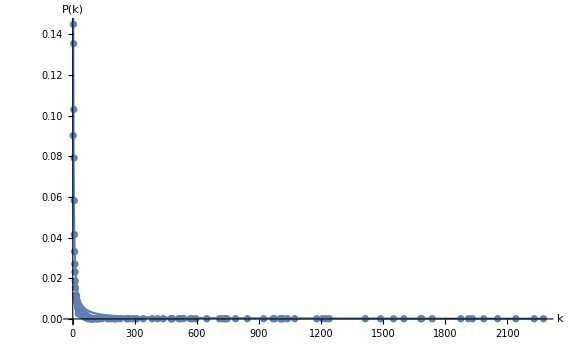

```mathematica
vis15=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"v-11.eps",vis15];
```

## Mean degree

```mathematica
degree=VertexDegree[igv15]//Mean//N
```

16.9927

## Record result

```mathematica
AppendTo[results, Flatten[{"visibility", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

## Horizontal Visibility Graph

```mathematica
horLinks=horizontalVisibility[series];
```

## Graph

```mathematica
igh15=Graph[horLinks, VertexLabels->"Name",DirectedEdges->False,VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igh15];
```

```mathematica
count = Total[adj]//Counts
```

<|2→3364,5→964,3→2213,8→285,10→138,4→1466,6→679,7→453,9→191,11→91,12→62,14→25,15→7,13→38,17→5,16→12,19→2,20→3,18→1|>

```mathematica
count[1]=.
```

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}]
```

{{2,3364/9999},{5,964/9999},{3,2213/9999},{8,95/3333},{10,46/3333},{4,1466/9999},{6,679/9999},{7,151/3333},{9,191/9999},{11,91/9999},{12,62/9999},{14,25/9999},{15,7/9999},{13,38/9999},{17,5/9999},{16,4/3333},{19,2/9999},{20,1/3333},{18,1/9999}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[1.06805/x^1.58078]

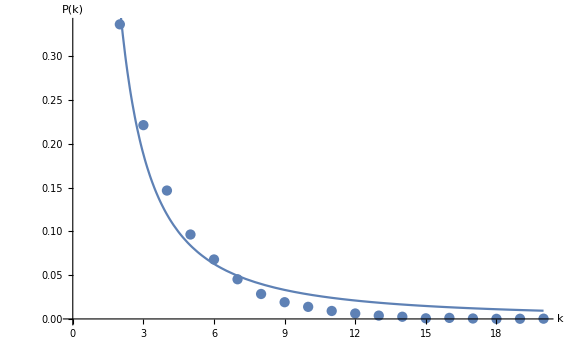

```mathematica
hvis15=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"hv-11.eps",hvis15];
```

## Mean degree

```mathematica
degree=VertexDegree[igh15]//Mean//N
```

3.9766

## Record result

```mathematica
AppendTo[results, Flatten[{"horizontal", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

## Return result

```mathematica
results
```

{{visibility,15,9999,16.9927,1.00841 ± 0.0921709,0.309897 ± 0.0459789},{horizontal,15,9999,3.9766,1.58078 ± 0.194003,1.06805 ± 0.211574}}